```mathematica
perfectQ[n_]:=(2n==Total[Divisors[n]])
```

```mathematica
Select[Range[10000],perfectQ]
```

{6,28,496,8128}

```mathematica
primesToN[n_]:=Select[Range[n],PrimeQ]
primeTwinQ[n_]:=PrimeQ[n+2]
```

```mathematica
s1=Select[primesToN[1000],primeTwinQ];
Transpose[AppendTo[{s1},Plus[s1,2]]]
```

{{3,5},{5,7},{11,13},{17,19},{29,31},{41,43},{59,61},{71,73},{101,103},{107,109},{137,139},{149,151},{179,181},{191,193},{197,199},{227,229},{239,241},{269,271},{281,283},{311,313},{347,349},{419,421},{431,433},{461,463},{521,523},{569,571},{599,601},{617,619},{641,643},{659,661},{809,811},{821,823},{827,829},{857,859},{881,883}}

```mathematica
data1 = {{1,3},{2,5},{3,8},{4,13}};
Simplify[InterpolatingPolynomial[data1,x]]
```

1/6 (6+14 x-3 x^2+x^3)

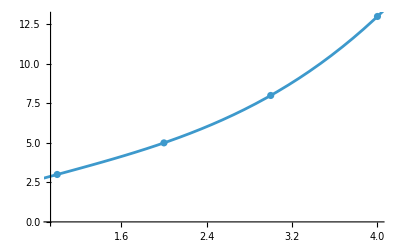

```mathematica
Show[ListPlot[data1],Plot[,{x, 0, 5}]]
```

```mathematica
Clear[x]
NDSolveValue[{x''[t]==-Sin[x[t]],x[0]==3.1,x'[0]==0},x[t],{t,0,20}]
NDSolveValue[{x''[t]==-Sin[x[t]],x[0]==3.2,x'[0]==0},x[t],{t,0,20}]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

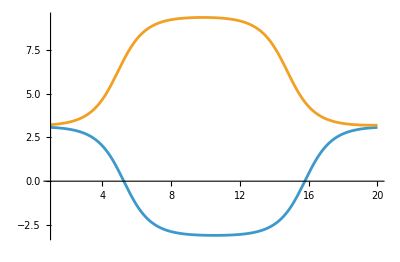

```mathematica
Plot[{,},{t,1,20},AspectRatio->Full]
```

```mathematica
NDSolveValue[{x'[t]==10(y[t]-x[t]),y'[t]==28x[t]-y[t]-z[t]*x[t],z'[t]==-8/3z[t]+x[t]*y[t],x[0]==5,y[0]==5,z[0]==5},{x[t],y[t],z[t]},{t,0,50}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
ParametricPlot3D[,{t,0,50}]
```

-Graphics3D-

```mathematica
Clear[primeFibonacci]
primeFibonacci[data2_]:=Select[data2,PrimeQ->"Index"]
```

```mathematica
primeFibonacci[Fibonacci[Range[200]]]
```

{3,4,5,7,11,13,17,23,29,43,47,83,131,137}

```mathematica
dvojice=Select[Flatten[Table[{i,j},{i,1,100},{j,1,100}],1],Divisible[(#[[1]]+#[[2]])!,#[[1]]!+#[[2]]!]&]
```

{{1,1},{1,2},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{3,5},{4,3},{4,4},{4,5},{5,3},{5,4},{5,5},{5,6},{6,5},{6,6},{6,7},{7,6},{7,7},{7,8},{8,7},{8,8},{8,9},{8,10},{9,8},{9,9},{9,10},{10,8},{10,9},{10,10},{10,11},{10,12},{11,10},{11,11},{11,12},{11,14},{12,10},{12,11},{12,12},{12,13},{13,12},{13,13},{13,14},{14,11},{14,13},{14,14},{14,15},{15,14},{15,15},{15,16},{15,17},{16,15},{16,16},{16,17},{17,15},{17,16},{17,17},{17,18},{17,19},{18,17},{18,18},{18,19},{19,17},{19,18},{19,19},{19,20},{20,19},{20,20},{20,21},{21,20},{21,21},{21,22},{21,23},{22,21},{22,22},{22,23},{23,21},{23,22},{23,23},{23,24},{24,23},{24,24},{24,25},{24,26},{25,24},{25,25},{25,26},{25,27},{26,24},{26,25},{26,26},{26,27},{27,25},{27,26},{27,27},{27,28},{28,27},{28,28},{28,29},{29,28},{29,29},{29,30},{29,31},{30,29},{30,30},{30,31},{31,29},{31,30},{31,31},{31,32},{32,31},{32,32},{32,33},{33,32},{33,33},{33,34},{34,33},{34,34},{34,35},{35,34},{35,35},{35,36},{35,37},{36,35},{36,36},{36,37},{36,38},{37,35},{37,36},{37,37},{37,38},{38,36},{38,37},{38,38},{38,39},{39,38},{39,39},{39,40},{40,39},{40,40},{40,41},{41,40},{41,41},{41,42},{42,41},{42,42},{42,43},{43,42},{43,43},{43,44},{44,43},{44,44},{44,45},{45,44},{45,45},{45,46},{46,45},{46,46},{46,47},{46,48},{47,46},{47,47},{47,48},{48,46},{48,47},{48,48},{48,49},{48,50},{49,48},{49,49},{49,50},{50,48},{50,49},{50,50},{50,51},{50,54},{51,50},{51,51},{51,52},{52,51},{52,52},{52,53},{53,52},{53,53},{53,54},{54,50},{54,53},{54,54},{54,55},{54,56},{55,54},{55,55},{55,56},{55,57},{56,54},{56,55},{56,56},{56,57},{57,55},{57,56},{57,57},{57,58},{57,60},{58,57},{58,58},{58,59},{59,58},{59,59},{59,60},{60,57},{60,59},{60,60},{60,61},{60,62},{61,60},{61,61},{61,62},{62,60},{62,61},{62,62},{62,63},{62,64},{63,62},{63,63},{63,64},{63,65},{64,62},{64,63},{64,64},{64,65},{65,63},{65,64},{65,65},{65,66},{66,65},{66,66},{66,67},{66,68},{67,66},{67,67},{67,68},{67,69},{68,66},{68,67},{68,68},{68,69},{69,67},{69,68},{69,69},{69,70},{70,69},{70,70},{70,71},{71,70},{71,71},{71,72},{72,71},{72,72},{72,73},{73,72},{73,73},{73,74},{73,75},{74,73},{74,74},{74,75},{75,73},{75,74},{75,75},{75,76},{76,75},{76,76},{76,77},{77,76},{77,77},{77,78},{78,77},{78,78},{78,79},{78,80},{78,82},{79,78},{79,79},{79,80},{80,78},{80,79},{80,80},{80,81},{80,82},{81,80},{81,81},{81,82},{82,78},{82,80},{82,81},{82,82},{82,83},{83,82},{83,83},{83,84},{84,83},{84,84},{84,85},{85,84},{85,85},{85,86},{86,85},{86,86},{86,87},{86,88},{87,86},{87,87},{87,88},{88,86},{88,87},{88,88},{88,89},{89,88},{89,89},{89,90},{90,89},{90,90},{90,91},{90,94},{91,90},{91,91},{91,92},{92,91},{92,92},{92,93},{93,92},{93,93},{93,94},{94,90},{94,93},{94,94},{94,95},{95,94},{95,95},{95,96},{95,97},{96,95},{96,96},{96,97},{97,95},{97,96},{97,97},{97,98},{98,97},{98,98},{98,99},{99,98},{99,99},{99,100},{100,99},{100,100}}

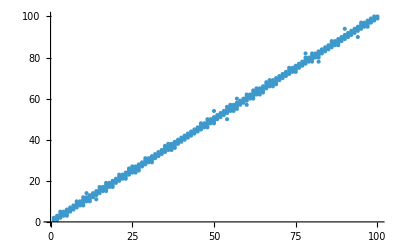

```mathematica
ListPlot[dvojice]
```

```mathematica
aproximace=FindFit[dvojice,a*x+b,{a,b},x]
```

{a→0.99908,b→0.0462571}

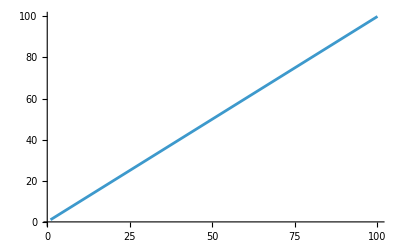

```mathematica
Plot[a*x+b/.,{x,1,100}]
```

```mathematica
Clear[maxima]
maxima[s_List]:=s//.{a___,b_,c_,d___}/;c<=b->{a,b,d}
```

```mathematica
maxima[Range[100]]
maxima[Reverse[Range[100]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

{100}

```mathematica
"Funkce odmázává hodnoty do té doby, než je seznam rostoucí"
```

```mathematica
Clear[fu]
fu[1]=34;
fu[2]=5;
fu[k3_/;Mod[k3,3]==0]:=10fu[k3/3]+76
fu[k3_/;Mod[k3,3]==1]:=10fu[(k3-1)/3]-2
fu[k3_/;Mod[k3,3]==2]:=10fu[(k3-2)/3]+8
Attributes[fu]={Listable};
```

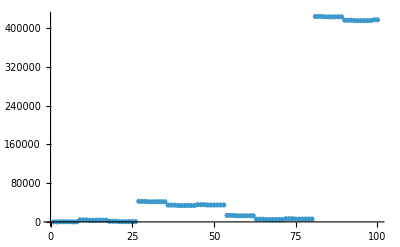

```mathematica
ListPlot[fu[Range[100]]]
```

```mathematica
ntyJeMaxQ[seznam_ ]:=seznam[[Length[seznam]]]==Max[Flatten[seznam]]
```

```mathematica
Select[Range[100],ntyJeMaxQ[fu[Range[#]]]&]
```

{1,3,9,27,81}

```mathematica
fu10000=fu[Range[10000]];
Select[Range[10000],ntyJeMaxQ[fu10000[[1;;#]]]&]
```

{1,3,9,27,81,243,729,2187,6561}

```mathematica
komprese[seznam_]:=Map[{#,1}&,seznam]//.{a___,{b_,numb_},c___,{d_,numd_},e___}/;b==d->{a,{b,numb+numd},c,e}
```

```mathematica
komprese[{1,1,1,1,3,3,"text","text"}]
```

{{1,4},{3,2},{text,2}}